```mathematica
(*code modified from Eduardo Sandoval/Jian Liu*)
```

### Dump

```mathematica
(*
here is the algorithm:

take the contourlength = 1000π; we discretize contourlength into numberofsteps 'numsteps';
we already have defined σ and κ. laplace pressure is defined by - 2σ/initial_radius where initial_radius is (contourlength/π);
ζ0(0) and δ0(1/initial_radius) are assumed from a spherical case. phaseboundaryfraction is the fraction of the contour for which different values of σ and κ are defined (over here 1/2 of the contour length).
phaseboundary is the total step number for the first phase boundary. contourlengthvector is the vector defining the contourlength as {0, .... , 1000π}
we define radius, height, membraneangle θ, membraneslope δ, membranecurvature ζ and membranejerk ϱ vectors as 0 vectors with the same length as contourvectorlength.

we define the first element of radius[[1]] and `iterativeradius` with initialradius, first element of height[[1]] and `iterativeheight` as 0. membraneangle[[1]] = π/2. membraneslope[[1]]=δ0 and membranecurvature[[1]]=ζ0;

we use these to compute membrane jerk;
ϱ=-1/2 δ^3-2 Cos[θ]/r ζ+(3/2 Sin[θ]/r)δ^2+((3 Cos[θ]^2-1)/(2 r^2))δ-(Cos[θ]^2+1)/(2 r^3)Sin[θ]+(σ/κ)(δ+Sin[θ]/r)+dP/κ;
iterating over the other elements.

Main loop(2:Length of contourvectorlength){
   IF	j==2:

	  use values at 'x'[[1]] to compute θ[[2]],δ[[2]] and ζ[[2]]. it is used to compute new interativeradius and new iterativeheight from θ[[2]] and the values are stored in r[[2]] and h[[2]]. compute ϱ[[2]] using θ[[2]], δ[[2]] and ζ[[2]].

ELSE IF  j<=IntegerPart[numsteps/2]+1 (essentially j from 3 to <= 1001)

		IF j<=IntegerPart[phaseboundary]+1
				
				if condition on membrane angle:

			   else:
			compute δ[[j]] and ζ[[j]] from the two previous values j-1 and j-2;
       compute iterativeradius and iterativeheight from current membrane angle and save values in radius[[j]] and height[[j]]. finally compute ϱ[[j]]

		 Else IF IntegerPart[phaseboundary]+2
				   (*this means we have reached our phase transition point: this part of code should not run*)

		 Else
				code should not run here as well
					

 ELSE IF  j == IntegerPart[numsteps/2]+2 (1002)
             (*halfway through the simulation. we need to backcalculate from here by defining `i` a dummy variable*)
		  i = numstep/2; (1000)
			  set θ[[1001;;]]=θ[[1;;1001]]; similar for δ, ζ, and ϱ, same for height and radius. set the initial θ[[1;;1001]] etc.. to zero.
            compute membrane angle[[1000]] from θ[[1002]] and δ[[1001]];
			  set iterativeradius to initialradius and update iterativeradius using θ[[1000]]
			set radius[[1000]] to iterativeradius. Likewise, for iterativeheight, first set to 0 then update it from θ[[1000]]. set height[[1000]] to iterative height.
compute δ[[1000]], membrane curvature[[1000]] from values stored at 1002 and 1001. compute ϱ[[1000]] using σ[[2]] and κ[[2]];
	
	  ELSE:
		 compute θ[[i]] from θ[[i+2]] and δ[[i+1]];
          iterativeradius and iterativeheight from θ[[i]] and set radius[[i]] and height[[i]] to iterativeradius/height;
		  compute δ[[i]] and ζ[[i]] from values at X[[i+1]] and X[[i+2]];
          compute ϱ[[i]];	  
}
*)
```

```mathematica
(*defining parameters*)
```

```mathematica
Quiet@Remove["Global`*"];
ClearAll["Global`*"];
```

```mathematica
(*contour length defines the length of our simulation in nm. Since we are in the 1D axisymmetric case, the total contour length is half of the vesicles total circumference in 2D
*)
```

```mathematica
ℂ=1000 π;
```

```mathematica
(*number of steps defines how many total steps we will take to simulate across the contour length. Together with the ℂ, these two parameters will define the resolution of our simulated shape*)
nsteps=2000;
```

```mathematica
(*this next param defines the fraction of the total that each respective phase in the two-phase separated vesicle will take up. For example, if it is switched to 1/3, the first phase will e defined for 1/3 of the contour with the second pahse defining the remainder. The excel file provided considers phase boundaries at 1/2 of the contour for all cases.
*)
```

```mathematica
(*the vesicle has two phases with potentially varying membrane tension and bending modulus. Both are initialized*)
```

```mathematica
σ={1/10,1/10}; (*pN/nm*)
κ={16000,16000 }; (*pN nm*)
```

```mathematica
(*we define the pressure this way as it presupposes a perfectly spherical vesicle. If one used a perfect circle and substituted the arc length formula into the shape equation, one is able to solve for pressure and obtain the laplace pressure formula below*)
```

```mathematica
Ρ=-2 σ[[1]]/(ℂ/π); (*pN/nm^2*)
```

```mathematica
(*finding a solution to the shape equation for one set of parameters when generating these plots, its best to set extrapolation to false at first, while using the shooting-and-match method to solve the differential equations, and extrapolate only after a valid solution is found*)
```

```mathematica
extrapolation=True;
extrapolationnumber=10;(*55;*)
```

```mathematica
(*these three parameters must be determined empirically for each set of parameters defining a vesicle. In the perfectly spherical case, the slope is constant and slope = 1/(ℂ/π) = 1/radius. Additionally in the perfectly spherical case, the curvature is 0 and lastly since we begin at the maximum radius, the initial radius is (ℂ/π), since the ℂ is half the circumference of the vesicle. As a result our guesses are varied from these starting values, regardless of the conditions. *)
```

```mathematica
ρ0=ℂ/π;
δ0=1/(ℂ/π);
ζ0=0;
```

```mathematica
data=Import["C:\\Users\\hashmial\\Downloads\\nuclei curvature and dP fit estimates\\dump\\phase_separated_GUV-main\\phase_separated_GUV-main\\shape.xlsx","Data"][[1]];
```

```mathematica
{headings,data}={First@data,Rest@data};
```

```mathematica
initialslopelist=data[[All,1]];
initialcurvaturelist=data[[All,2]];
sigmalist=data[[All,3]];
Ρlist=data[[All,4]];
baselinesigma=0.1;
baselineΡ=-2 baselinesigma/(ℂ/π);
initialradiilist=data[[All,5]];
extrapolationnumbers=data[[All,6]];
```

```mathematica
(*
before explaining the function as we proceed, there are two gripes:
it is important to note that the magic number I chose is estimated to be 3000, the maximum diameter seen when I originally solved all these vesicles of varying membrane tension and Ρ. Ideally, we would like to obtain this from the list of solutions, but due to differing amounts of extrapolation, the solutions will all have a different size despite the same ℂ. As such, we will likely run into errors if I tried to make a matrix of all solutions and finding the maximum difference of each  solution. I'm sure there is some function that must be able to interpolate in between smaller solutions and lengthen them to a desired length, but I got lazy.

Second is the spacing parameter. This defines what is the minimal proportional variation of Ρ or membrane tension used. Again, ideally we would like to just obtain this from the list of Ρ and membrane tensions used, but I got lazy. Since baseline membrane tensions and Ρ are used, an improvement might be to just compare the values of membrane tensions and Ρ to the baselines and find the minimum proportional difference. With this space parameter, I also find issue that the code in its current state requires that the spacing between Ρ and membrane tensions be similar, i.e. if we had a minimum proportional changes in Ρs as 0.2 but 0.1 for membrane tension, then the pahse plane will look more sparse as a result.


*)
```

```mathematica
Δs=ℂ/nsteps;
```

```mathematica
η=1/2;
```

```mathematica
ℋ=η (ℂ/Δs) ;
```

```mathematica
ℂvector=Subdivide[ℂ,nsteps];
```

```mathematica
θ=δ=ζ=ϱ=ρ=h=ConstantArray[0,Length@ℂvector];
```

```mathematica
(*
we use our initial guesses to commence simulation. we use these initial conditions to calculate membrane jerk as defined by our equation.
please note we start our simulation halfway through the ℂ, since the simulation is extremely unstable at small radii due to the 1/r^3 dependence.
*)
```

```mathematica
ρ[[1]]=ρ0;
ρiter=ρ0;
h[[1]]=0;
hiter=0.;
θ[[1]]=π/2;
δ[[1]]=δ0;
ζ[[1]]=ζ0;
(*this formula is the shape equation for the 1D axisymmetric vesicle and therefore it is not evaluated using any finite difference scheme*)
```

```mathematica
ϱ[[1]]=N[-1/2 δ[[1]]^3-2 Cos[θ[[1]]]/ρ[[1]] ζ[[1]]+3/2 Sin[θ[[1]]]/ρ[[1]] δ[[1]]^2+(3 Cos[θ[[1]]]^2-1)/(2 ρ[[1]]^2)δ[[1]]-(Cos[θ[[1]]]^2+1)/(2 ρ[[1]]^3)Sin[θ[[1]]]+σ[[1]]/κ[[1]](δ[[1]]+Sin[θ[[1]]]/ρ[[1]])+Ρ/κ[[1]]];
```

```mathematica
(*now we iterate*)
```

```mathematica
Do[
Which[j==2,
(*we use a central finite difference method, which results in a modified step for the second timestep of the simulation. we assume θ[[i-2]]=θ[[i-1]]*)
θ[[j]]=θ[[j-1]]+2 δ[[j-1]]*Δs;
δ[[j]]=δ[[j-1]]+2 ζ[[j-1]]*Δs;
ζ[[j]]=ζ[[j-1]]+2 ϱ[[j-1]]*Δs;
(*we update the radius and height for each step, this is estimated by using trigonometry and assuming that our Δs is small enough that this error will not be far off*)
ρiter+=N@Δs*Cos[θ[[j]]]//N;
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]]//N;
h[[j]]=hiter;
(*again we have the shape equation*)
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[1]]/κ[[1]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[1]]];
,

j<=IntegerPart[nsteps/2]+1,

Which[j<=IntegerPart[ℋ]+1,
θ[[j]]=θ[[j-2]]+2*δ[[j-1]]*Δs;

(*this if loop is purely for debugging and seeing where a simulation breaks to adjust guesses*)
If[θ[[j]]>2 π || θ[[j]]<-2π,
Print@j;
δ[[j]]=δ[[j-2]]+2 ζ[[j-1]]*Δs;
ζ[[j]]=ζ[[j-2]]+2 ϱ[[j-1]]*Δs;
ρiter+= N@Δs*Cos[θ[[j]]];
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]];
h[[j]]=hiter;
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[1]]/κ[[1]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[1]]];
Continue[],

δ[[j]]=δ[[j-2]]+ 2 ζ[[j-1]]*Δs;
ζ[[j]]=ζ[[j-2]]+2 ϱ[[j-1]]*Δs;
ρiter+=N@Δs*Cos[θ[[j]]];
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]];
h[[j]]=hiter;
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[1]]/κ[[1]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[1]]];
],
j==IntegerPart[ℋ]+2,
(*this is our first interesting step as we have reached our phase boundary or transition. Relevant formulae can be found in Jian Liu's paper: endocytic vesicle scission by lipid phase boundary forces*)
θ[[j]]=θ[[j-2]]+2 δ[[j-1]]*Δs;
ρiter+=N@Δs *Cos[θ[[j]]];
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]];
h[[j]]=hiter;
phase1δ=δ[[j-2]]-2 ζ[[j-1]]*Δs;
phase1ζ=ζ[[j-2]]-2 ϱ[[j-1]]*Δs;
phase2δ=κ[[1]]/κ[[2]] phase1δ-(Sin[θ[[j]]](κ[[2]]-κ[[1]]))/(κ[[2]] ρ[[j]]);
δ[[j]]=phase2δ;
phase2ζ=κ[[1]]/κ[[2]](phase1ζ-(Sin[θ[[j]]] Cos[θ[[j]]])/ρ[[j]]^2+Cos[θ[[j]]] phase1δ/ρ[[j]])-(Cos[θ[[j]]]δ[[j]])/ρ[[j]]+(Sin[θ[[j]]]Cos[θ[[j]]])/ρ[[j]]^2;
ζ[[j]]=phase2ζ;
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[2]]/κ[[2]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[2]]];
,
True
,
θ[[j]]=θ[[j-2]]+2 δ[[j-1]]*Δs;
δ[[j]]=δ[[j-2]]+2 ζ[[j-1]] *Δs;
ζ[[j]]=ζ[[j-2]]+2ϱ[[j-1]]*Δs;
ρiter+=N@Δs*Cos[θ[[j]]];
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]];
h[[j]]=hiter;
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[2]]/κ[[2]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[2]]];
],
j==IntegerPart[nsteps/2]+2,
(*when we have reached halfway through the simulation, we have to back calculate the remaining half, since we began at half of the contour. We start by initializing a new index to make the computation easier, since now we are back calculating and will subtract the index by one each step *)
i=IntegerPart[nsteps/2];
(*we then take simulation results so far and define them as the second half of the solution i.e. we have a 1000 length vector and got to 500 and now must backcalculate, we redefined the last 500 of the vector to our current result *)
θ[[i+1;;]]=θ[[1;;j-1]];
ζ[[i+1;;]]=ζ[[1;;j-1]];
δ[[i+1;;]]=δ[[1;;j-1]];
ϱ[[i+1;;]]=ϱ[[1;;j-1]];
(*the bottom four lines may not be needed and are only used to placate paranoia that previously defined values are not refound and maintain
inaccuracies *)
θ[[1;;i]]=0;
ϱ[[1;;i]]=0;
ζ[[1;;i]]=0;
δ[[1;;i]]=0;

h[[i+1;;]]=h[[1;;j-1]];
ρ[[i+1;;]]=ρ[[1;;j-1]];
h[[1;;i]]=0;
ρ[[1;;i]]=0;
θ[[i]]=θ[[i+2]]-2δ[[i+1]]*Δs;
ρiter=ρ0;
ρiter-=N@Δs*Cos[θ[[i]]];
ρ[[i]]=ρiter;
hiter=0;
hiter-=N@Δs*Sin[θ[[i]]];
h[[i]]=hiter;

If[i==IntegerPart[ℋ]+2,
phase1δ=δ[[i+2]]-2 ζ[[i+1]]Δs;
phase1ζ=ζ[[i+2]]-2 ϱ[[i+1]]Δs;
phase2δ=κ[[1]]/κ[[2]] phase1δ-(Sin[θ[[i]]](κ[[2]]-κ[[1]]))/(κ[[2]]ρ[[i]]);
δ[[i]]=phase2δ;
phase2ζ=κ[[1]]/κ[[2]](phase1ζ-(Sin[θ[[i]]]Cos[θ[[i]]])/ρ[[i]]^2+Cos[θ[[i]]] phase1δ/ρ[[i]])-(Cos[θ[[i]]]δ[[i]])/ρ[[i]]+(Sin[θ[[i]]]Cos[θ[[i]]])/ρ[[i]]^2;
ζ[[i]]=phase2ζ;
(*note that since we are in the second phase, the membrane shape is now using the second measurements of membrane tension and binding modulus*)
ϱ[[i]]=N[-1/2 δ[[i]]^3-2 Cos[θ[[i]]]/ρ[[i]] ζ[[i]]+3/2 Sin[θ[[i]]]/ρ[[i]] δ[[i]]^2+(3 Cos[θ[[i]]]^2-1)/(2 ρ[[i]]^2)δ[[i]]-(Cos[θ[[i]]]^2+1)/(2 ρ[[i]]^3)Sin[θ[[i]]]+σ[[2]]/κ[[2]](δ[[i]]+Sin[θ[[i]]]/ρ[[i]])+Ρ/κ[[2]]];
,

δ[[i]]=δ[[i+2]]-2 ζ[[i+1]]Δs;
ζ[[i]]=ζ[[i+2]]-2 ϱ[[i+1]]Δs;
ϱ[[i]]=N[-1/2 δ[[i]]^3-2 Cos[θ[[i]]]/ρ[[i]] ζ[[i]]+3/2 Sin[θ[[i]]]/ρ[[i]] δ[[i]]^2+(3 Cos[θ[[i]]]^2-1)/(2 ρ[[i]]^2)δ[[i]]-(Cos[θ[[i]]]^2+1)/(2 ρ[[i]]^3)Sin[θ[[i]]]+σ[[2]]/κ[[2]](δ[[i]]+Sin[θ[[i]]]/ρ[[i]])+Ρ/κ[[2]]];
],

True,

i=i-1;
θ[[i]]=θ[[i+2]]-2δ[[i+1]]Δs;
If[θ[[i]]>2 π || θ[[i]]<-2 π,
Print@j;
Break[],

ρiter-=N@Δs*Cos[θ[[i]]];
hiter-=N@Δs*Sin[θ[[i]]];
δ[[i]]=δ[[i+2]]-2 ζ[[i+1]]Δs;
ζ[[i]]=ζ[[i+2]]-2 ϱ[[i+1]]Δs;
ρ[[i]]=ρiter;
h[[i]]=hiter;
ϱ[[i]]=N[-1/2 δ[[i]]^3-2 Cos[θ[[i]]]/ρ[[i]] ζ[[i]]+3/2 Sin[θ[[i]]]/ρ[[i]]*δ[[i]]^2+(3 Cos[θ[[i]]]^2-1)/(2 ρ[[i]]^2)δ[[i]]-(Cos[θ[[i]]]^2+1)/(2 ρ[[i]]^3)Sin[θ[[i]]]+σ[[2]]/κ[[2]](δ[[i]]+Sin[θ[[i]]]/ρ[[i]])+Ρ/κ[[2]]];
];
];
,{j,2,Length[ℂvector]}
];
```

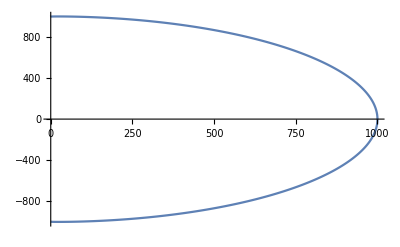

```mathematica
ListLinePlot[Thread[{ρ,h}]]
```

```mathematica
theta=θ;
slope=δ;
curvature=ζ;
```

```mathematica
ρ=;
h=;
```

```mathematica
interpolationnumber=extrapolationnumbers[[1]];
```

```mathematica
(*ListLinePlot[{radius[[1;;IntegerPart[ℋfraction*nsteps]]],Abs[radius[[1;;IntegerPart[ℋfraction*nsteps]]]-interpolationnumber]},PlotStyle->{Red,Blue}];*)
```

```mathematica
(*ListLinePlot[{radius[[IntegerPart[ℋfraction*nsteps];;nsteps+1]],radius[[IntegerPart[ℋfraction*nsteps];;nsteps+1]]-interpolationnumber},PlotStyle->{Red,Blue}];*)
```

```mathematica
If[True,
(*to extrapolate we first take whatever our extrapolation number is defined as interpolation number because when we consider the total vesicle/cell, technically we are just interpolating as we are filling in between known points), and find the minimum index for either end of the contour that corresponds to this value *)
closestIndex=First@Flatten@Position[#,Min@#]&@Abs[ρ[[IntegerPart[η*nsteps];;nsteps+1]]-interpolationnumber];closestIndex2=First@Flatten@Position[#,Min@#]&@Abs[ρ[[1;;IntegerPart[η*nsteps]]]-interpolationnumber];
(*we use the index to construct a new vector and thus solution that reflects the rest of the solution about the y axis and generates a vector to fill in the rest*)
ρ=ρ[[closestIndex2;;closestIndex+η*nsteps]];
h=h[[closestIndex2;;closestIndex+η*nsteps]];

(*for first interpolation we use newradius and newheight*)
ρnew=ConstantArray[0,2Length[ρ]];
ρnew[[1;;Length@ρ]]=ρ;
ρnew[[Length[ρ]+1;;]]=-Reverse[ρ];

hnew=ConstantArray[0,2 Length[h]];
hnew[[1;;Length@h]]=h;
hnew[[Length[h]+1;;]]=Reverse[h];

interpolationpts=Range[-interpolationnumber,interpolationnumber,Δs];

interpolationFn=Interpolation[Thread[{ρnew[[Length[ρnew]/2 -interpolationnumber;;Length[ρnew]/2 +interpolationnumber]],hnew[[Length[ρnew]/2 -interpolationnumber;;Length[ρnew]/2 +interpolationnumber]]}],Method->"Spline"];

interpolation=Table[interpolationFn[x],{x,interpolationpts}];
(*for second interpolation we use interpradius and interpheight*)
ρinterp=ConstantArray[0,2Length@ρ];
ρinterp[[1;;Length@ρ]]=Reverse@ρ;
ρinterp[[Length[ρ]+1;;]]=-ρ;
hinterp=ConstantArray[0,2Length@ρ];
hinterp[[1;;Length@h]]=Reverse@h;
hinterp[[Length[h]+1;;]]=h;

interpolationFn2=Interpolation[Thread[{ρinterp[[Length[ρnew]/2 -interpolationnumber;;Length[ρnew]/2 +interpolationnumber]],hinterp[[Length[ρnew]/2 -interpolationnumber;;Length[ρnew]/2 +interpolationnumber]]}],Method->"Spline"];
interpolation2=Table[interpolationFn2[x],{x,interpolationpts}];

(*final vectors with interpolations incorporated*)
ρnewf=ConstantArray[0,2Length[ρ]+2Length[interpolationpts]];
ρnewf[[1;;Length[interpolationpts]]]=interpolationpts;
ρnewf[[Length[interpolationpts]+1;;Length[ρ]+Length[interpolationpts]]]=ρ;
ρnewf[[Length[ρ]+Length[interpolationpts]+1;;Length[ρ]+2Length[interpolationpts]]]=-interpolationpts;ρnewf[[Length[ρ]+2Length[interpolationpts]+1;;2Length[ρ]+2Length[interpolationpts]]]=-Reverse[ρ];

hnewf=ConstantArray[0,2Length[ρ]+2Length[interpolationpts]];
hnewf[[1;;Length[interpolationpts]]]=interpolation2;
hnewf[[Length[interpolationpts]+1;;Length[ρ]+Length@interpolationpts]]=h;hnewf[[Length[ρ]+Length[interpolationpts]+1;;Length[ρ]+2Length[interpolationpts]]]=interpolation;hnewf[[Length[ρ]+2Length[interpolationpts]+1;;2Length[ρ]+2Length[interpolationpts]]]=Reverse[h];

ρ=ρnewf;
h=hnewf;
];
```

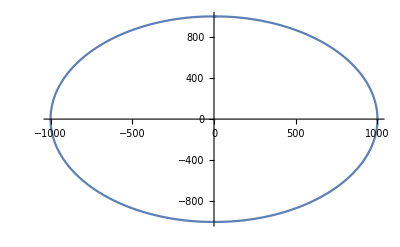

```mathematica
Thread[{ρ,h}]//ListLinePlot
```

# Mains()

```mathematica
Quiet@Remove["Global`*"];Quiet@ClearAll["Global`*"];
```

```mathematica
Clear@interpmembraneProfile;
interpmembraneProfile[ρ_,h_,η_,Δs_,nsteps_,interpolationnumber_]:=Block[{index1,index2,ρc,hc,ρnew,hnew,interpolationpts,interpolationFn,interpolation,ρinterp,hinterp,interpolationFn2,interpolation2,ρnewf,hnewf},

If[True,
(*to extrapolate we first take whatever our extrapolation number is defined as interpolation number because when we consider the total vesicle/cell, technically we are just interpolating as we are filling in between known points), and find the minimum index for either end of the contour that corresponds to this value *)
index1=First@Flatten@Position[#,Min@#]&@Abs[ρ[[IntegerPart[η*nsteps];;nsteps+1]]-interpolationnumber];index2=First@Flatten@Position[#,Min@#]&@Abs[ρ[[1;;IntegerPart[η*nsteps]]]-interpolationnumber];
(*we use the index to construct a new vector and thus solution that reflects the rest of the solution about the y axis and generates a vector to fill in the rest*)
ρc=ρ[[index2;;index1+η*nsteps]];
hc=h[[index2;;index1+η*nsteps]];

(*for first interpolation we use newradius and newheight*)
ρnew=ConstantArray[0,2Length[ρc]];
ρnew[[1;;Length@ρc]]=ρc;
ρnew[[Length[ρc]+1;;]]=-Reverse[ρc];

hnew=ConstantArray[0,2 Length[hc]];
hnew[[1;;Length@hc]]=hc;
hnew[[Length[hc]+1;;]]=Reverse[hc];

interpolationpts=Range[-interpolationnumber,interpolationnumber,Δs];

interpolationFn=Interpolation[Thread[{ρnew[[Length[ρnew]/2 -interpolationnumber;;Length[ρnew]/2 +interpolationnumber]],hnew[[Length[ρnew]/2 -interpolationnumber;;Length[ρnew]/2 +interpolationnumber]]}],Method->"Spline",InterpolationOrder->2];

interpolation=Table[interpolationFn[x],{x,interpolationpts}];
(*for second interpolation we use interpradius and interpheight*)
ρinterp=ConstantArray[0,2Length@ρc];
ρinterp[[1;;Length@ρc]]=Reverse@ρc;
ρinterp[[Length[ρc]+1;;]]=-ρc;
hinterp=ConstantArray[0,2Length@ρc];
hinterp[[1;;Length@hc]]=Reverse@hc;
hinterp[[Length[hc]+1;;]]=hc;

interpolationFn2=Interpolation[Thread[{ρinterp[[Length[ρnew]/2 -interpolationnumber;;Length[ρnew]/2 +interpolationnumber]],hinterp[[Length[ρnew]/2 -interpolationnumber;;Length[ρnew]/2 +interpolationnumber]]}],Method->"Spline",InterpolationOrder->2];
interpolation2=Table[interpolationFn2[x],{x,interpolationpts}];

(*final vectors with interpolations incorporated*)
ρnewf=ConstantArray[0,2Length[ρc]+2Length[interpolationpts]];
ρnewf[[1;;Length[interpolationpts]]]=interpolationpts;
ρnewf[[Length[interpolationpts]+1;;Length[ρc]+Length[interpolationpts]]]=ρc;
ρnewf[[Length[ρc]+Length[interpolationpts]+1;;Length[ρc]+2Length[interpolationpts]]]=-interpolationpts;ρnewf[[Length[ρc]+2Length[interpolationpts]+1;;2Length[ρc]+2Length[interpolationpts]]]=-Reverse[ρc];

hnewf=ConstantArray[0,2Length[ρc]+2Length[interpolationpts]];
hnewf[[1;;Length[interpolationpts]]]=interpolation2;
hnewf[[Length[interpolationpts]+1;;Length[ρc]+Length@interpolationpts]]=hc;hnewf[[Length[ρc]+Length[interpolationpts]+1;;Length[ρc]+2Length[interpolationpts]]]=interpolation;hnewf[[Length[ρc]+2Length[interpolationpts]+1;;2Length[ρc]+2Length[interpolationpts]]]=Reverse[hc];

{ρnewf,hnewf}
]
];
```

```mathematica
Clear@membraneShapeFn;
membraneShapeFn[ℂ_,nsteps_,η_,δ0_,ζ0_,ρ0_,σ_,κ_,Ρ_,extrap_:True|False,interpolationnumber_]:=Block[{θ,δ,ζ,ϱ,ρ,h,Δs,ℂvector,ℋ,ρiter,hiter},
Δs=ℂ/nsteps;
ℋ=η (ℂ/Δs) ;
ℂvector=Subdivide[ℂ,nsteps];
θ=δ=ζ=ϱ=ρ=h=ConstantArray[0,Length@ℂvector];

ρ[[1]]=ρ0;
ρiter=ρ0;
h[[1]]=0;
hiter=0.;
θ[[1]]=π/2;
δ[[1]]=δ0;
ζ[[1]]=ζ0;

ϱ[[1]]=N[-1/2 δ[[1]]^3-2 Cos[θ[[1]]]/ρ[[1]] ζ[[1]]+3/2 Sin[θ[[1]]]/ρ[[1]] δ[[1]]^2+(3 Cos[θ[[1]]]^2-1)/(2 ρ[[1]]^2)δ[[1]]-(Cos[θ[[1]]]^2+1)/(2 ρ[[1]]^3)Sin[θ[[1]]]+σ[[1]]/κ[[1]](δ[[1]]+Sin[θ[[1]]]/ρ[[1]])+Ρ/κ[[1]]];

Do[
Which[j==2,
(*we use a central finite difference method, which results in a modified step for the second timestep of the simulation. we assume θ[[i-2]]=θ[[i-1]]*)
θ[[j]]=θ[[j-1]]+2 δ[[j-1]]Δs;
δ[[j]]=δ[[j-1]]+2 ζ[[j-1]]Δs;
ζ[[j]]=ζ[[j-1]]+2 ϱ[[j-1]]Δs;
(*we update the radius and height for each step, this is estimated by using trigonometry and assuming that our Δs is small enough that this error will not be far off*)
ρiter+=Δs*Cos[θ[[j]]]//N;
ρ[[j]]=ρiter;
hiter+=Δs*Sin[θ[[j]]]//N;
h[[j]]=hiter;
(*again we have the shape equation*)
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[1]]/κ[[1]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[1]]];
,

j<=IntegerPart[nsteps/2]+1,

Which[j<=IntegerPart[ℋ]+1,
θ[[j]]=θ[[j-2]]+2*δ[[j-1]]*Δs;

(*this if loop is purely for debugging and seeing where a simulation breaks to adjust guesses*)
If[θ[[j]]>2 π || θ[[j]]<-2π,
(*this part should not run*)
Print@j;
δ[[j]]=δ[[j-2]]+2 ζ[[j-1]]Δs;
ζ[[j]]=ζ[[j-2]]+2 ϱ[[j-1]]Δs;
ρiter+= N@Δs*Cos[θ[[j]]];
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]];
h[[j]]=hiter;
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[1]]/κ[[1]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[1]]];
Continue[],

δ[[j]]=δ[[j-2]]+ 2 ζ[[j-1]]Δs;
ζ[[j]]=ζ[[j-2]]+2 ϱ[[j-1]]Δs;
ρiter+=N@Δs*Cos[θ[[j]]];
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]];
h[[j]]=hiter;
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[1]]/κ[[1]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[1]]];
],
j==IntegerPart[ℋ]+2,
(*this part should not run for our case*)
(*we have reached our phase boundary or transition. Relevant formulae can be found in Jian Liu's paper: endocytic vesicle scission by lipid phase boundary forces*)
θ[[j]]=θ[[j-2]]+2 δ[[j-1]]*Δs;
ρiter+=N@Δs *Cos[θ[[j]]];
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]];
h[[j]]=hiter;
phase1δ=δ[[j-2]]-2 ζ[[j-1]]Δs;
phase1ζ=ζ[[j-2]]-2 ϱ[[j-1]]Δs;
phase2δ=κ[[1]]/κ[[2]] phase1δ-(Sin[θ[[j]]](κ[[2]]-κ[[1]]))/(κ[[2]] ρ[[j]]);
δ[[j]]=phase2δ;
phase2ζ=κ[[1]]/κ[[2]](phase1ζ-(Sin[θ[[j]]] Cos[θ[[j]]])/ρ[[j]]^2+Cos[θ[[j]]] phase1δ/ρ[[j]])-(Cos[θ[[j]]]δ[[j]])/ρ[[j]]+(Sin[θ[[j]]]Cos[θ[[j]]])/ρ[[j]]^2;
ζ[[j]]=phase2ζ;
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[2]]/κ[[2]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[2]]];
,
True
,
θ[[j]]=θ[[j-2]]+2 δ[[j-1]]Δs;
δ[[j]]=δ[[j-2]]+2 ζ[[j-1]] Δs;
ζ[[j]]=ζ[[j-2]]+2ϱ[[j-1]]Δs;
ρiter+=N@Δs*Cos[θ[[j]]];
ρ[[j]]=ρiter;
hiter+=N@Δs*Sin[θ[[j]]];
h[[j]]=hiter;
ϱ[[j]]=N[-1/2 δ[[j]]^3-2 Cos[θ[[j]]]/ρ[[j]] ζ[[j]]+3/2 Sin[θ[[j]]]/ρ[[j]] δ[[j]]^2+(3 Cos[θ[[j]]]^2-1)/(2 ρ[[j]]^2)δ[[j]]-(Cos[θ[[j]]]^2+1)/(2 ρ[[j]]^3)Sin[θ[[j]]]+σ[[2]]/κ[[2]](δ[[j]]+Sin[θ[[j]]]/ρ[[j]])+Ρ/κ[[2]]];
],
j==IntegerPart[nsteps/2]+2,
(*when we have reached halfway through the simulation, we have to back calculate the remaining half, since we began at half of the contour. We start by initializing a new index to make the computation easier, since now we are back calculating and will subtract the index by one each step *)
i=IntegerPart[nsteps/2];
(*we then take simulation results so far and define them as the second half of the solution i.e. we have a 1000 length vector and got to 500 and now must backcalculate, we redefined the last 500 of the vector to our current result *)
θ[[i+1;;]]=θ[[1;;j-1]];
ζ[[i+1;;]]=ζ[[1;;j-1]];
δ[[i+1;;]]=δ[[1;;j-1]];
ϱ[[i+1;;]]=ϱ[[1;;j-1]];
(*the bottom four lines may not be needed and are only used to placate paranoia that previously defined values are not refound and maintain
inaccuracies *)
θ[[1;;i]]=0;
ϱ[[1;;i]]=0;
ζ[[1;;i]]=0;
δ[[1;;i]]=0;

h[[i+1;;]]=h[[1;;j-1]];
ρ[[i+1;;]]=ρ[[1;;j-1]];
h[[1;;i]]=0;
ρ[[1;;i]]=0;
θ[[i]]=θ[[i+2]]-2δ[[i+1]]*Δs;
ρiter=ρ0;
ρiter-=N@Δs*Cos[θ[[i]]];
ρ[[i]]=ρiter;
hiter=0;
hiter-=N@Δs*Sin[θ[[i]]];
h[[i]]=hiter;

If[i==IntegerPart[ℋ]+2,
(*this part should not run for our case*)
phase1δ=δ[[i+2]]-2 ζ[[i+1]]Δs;
phase1ζ=ζ[[i+2]]-2 ϱ[[i+1]]Δs;
phase2δ=κ[[1]]/κ[[2]] phase1δ-(Sin[θ[[i]]](κ[[2]]-κ[[1]]))/(κ[[2]]ρ[[i]]);
δ[[i]]=phase2δ;
phase2ζ=κ[[1]]/κ[[2]](phase1ζ-(Sin[θ[[i]]]Cos[θ[[i]]])/ρ[[i]]^2+Cos[θ[[i]]] phase1δ/ρ[[i]])-(Cos[θ[[i]]]δ[[i]])/ρ[[i]]+(Sin[θ[[i]]]Cos[θ[[i]]])/ρ[[i]]^2;
ζ[[i]]=phase2ζ;
(*note that since we are in the second phase, the membrane shape is now using the second measurements of membrane tension and binding modulus*)
ϱ[[i]]=N[-1/2 δ[[i]]^3-2 Cos[θ[[i]]]/ρ[[i]] ζ[[i]]+3/2 Sin[θ[[i]]]/ρ[[i]] δ[[i]]^2+(3 Cos[θ[[i]]]^2-1)/(2 ρ[[i]]^2)δ[[i]]-(Cos[θ[[i]]]^2+1)/(2 ρ[[i]]^3)Sin[θ[[i]]]+σ[[2]]/κ[[2]](δ[[i]]+Sin[θ[[i]]]/ρ[[i]])+Ρ/κ[[2]]];
,

δ[[i]]=δ[[i+2]]-2 ζ[[i+1]]Δs;
ζ[[i]]=ζ[[i+2]]-2 ϱ[[i+1]]Δs;
ϱ[[i]]=N[-1/2 δ[[i]]^3-2 Cos[θ[[i]]]/ρ[[i]] ζ[[i]]+3/2 Sin[θ[[i]]]/ρ[[i]] δ[[i]]^2+(3 Cos[θ[[i]]]^2-1)/(2 ρ[[i]]^2)δ[[i]]-(Cos[θ[[i]]]^2+1)/(2 ρ[[i]]^3)Sin[θ[[i]]]+σ[[2]]/κ[[2]](δ[[i]]+Sin[θ[[i]]]/ρ[[i]])+Ρ/κ[[2]]];
],

True,

i=i-1;
θ[[i]]=θ[[i+2]]-2δ[[i+1]]Δs;
If[θ[[i]]>2 π || θ[[i]]<-2 π,
Print@j;
Break[],

ρiter-=N@Δs*Cos[θ[[i]]];
hiter-=N@Δs*Sin[θ[[i]]];
δ[[i]]=δ[[i+2]]-2 ζ[[i+1]]Δs;
ζ[[i]]=ζ[[i+2]]-2 ϱ[[i+1]]Δs;
ρ[[i]]=ρiter;
h[[i]]=hiter;
ϱ[[i]]=N[-1/2 δ[[i]]^3-2 Cos[θ[[i]]]/ρ[[i]] ζ[[i]]+3/2 Sin[θ[[i]]]/ρ[[i]]*δ[[i]]^2+(3 Cos[θ[[i]]]^2-1)/(2 ρ[[i]]^2)δ[[i]]-(Cos[θ[[i]]]^2+1)/(2 ρ[[i]]^3)Sin[θ[[i]]]+σ[[2]]/κ[[2]](δ[[i]]+Sin[θ[[i]]]/ρ[[i]])+Ρ/κ[[2]]];
];
];
,{j,2,Length[ℂvector]}
];
{ρ,h};
If[extrap,interpmembraneProfile[ρ,h,η,Δs,nsteps,interpolationnumber]]
];
```

```mathematica
data=Import["C:\\Users\\hashmial\\Downloads\\nuclei curvature and dP fit estimates\\dump\\shape.xlsx","Data"][[1]];
```

```mathematica
{headings,data}={First@data,Rest@data};
```

```mathematica
initialslopelist=data[[All,1]];
initialcurvaturelist=data[[All,2]];
sigmalist=data[[All,3]];
Ρlist=data[[All,4]];
baselinesigma=0.1;
ℂ=1000 π;
baselineΡ=-2 baselinesigma/(ℂ/π);
initialradiilist=data[[All,5]];
extrapolationnumbers=data[[All,6]];
```

```mathematica
Clear@membraneShapePhasePlane;
membraneShapePhasePlane[]:=Block[{},
maxradius=minradius=maxheight=minheight=0;
ℂ=1000 π;
nsteps=2000;

η=1/2;
κ={16000,16000};
σ={1/10,1/10};
Ρ=-2 σ[[1]]/(ℂ/π);
extrapolation=True;
interpolationnumber=10;

ρ0=ℂ/π;
δ0=1/(ℂ/π);
ζ0=0;
spacing=0.2;
magicnum=3000;
(* rest of the code comes here*)
Table[

σ={baselinesigma,sigmalist[[l]]};
δ0=initialslopelist[[l]];
ζ0=initialcurvaturelist[[l]];
ρ0=initialradiilist[[l]];
Ρ=Ρlist[[l]];
interpolationnumber=extrapolationnumbers[[l]];
{radius,height}=membraneShapeFn[ℂ,nsteps,η,δ0,ζ0,ρ0,σ,κ,Ρ,True,interpolationnumber];

(*changeinrad=(sigmalist[[l]]-baselinesigma)/(baselinesigma spacing)*magicnum;

changeinheight=(Ρ-baselineΡ)/(baselineΡ spacing)*magicnum;


height+=changeinheight;

radius+=changeinrad;*)

If[extrapolation,{sigmalist[[l]]/baselinesigma,Ρ/baselineΡ,
(*ListLinePlot[Thread@{radius,height},AspectRatio->{1,1},Axes->False,ImageSize->Tiny,MaxPlotPoints->200,InterpolationOrder->1,PlotStyle->RandomColor[]],*)Graphics[{FaceForm[Directive[Opacity[0.2],RandomColor[]]],EdgeForm[Directive[Black]],FilledCurve[BSplineCurve[Thread[{radius,height}],SplineClosed->True]]},ImageSize->Tiny],
Graphics[{FaceForm[Directive[RGBColor[0.255,0.333,0.902,0.2]]],EdgeForm[Directive[Black]],FilledCurve[BSplineCurve[Thread[{radius,height}],SplineClosed->True]]},ImageSize->Tiny]
}]
,{l,Length[Ρlist]}
]

];
```

```mathematica
res=membraneShapePhasePlane[];
```

```mathematica
res1=SortBy[res,First]
```

{{0.8,0.8,-Graphics-,-Graphics-},{0.8,1.,-Graphics-,-Graphics-},{0.8,1.2,-Graphics-,-Graphics-},{1.,0.8,-Graphics-,-Graphics-},{1.,1.,-Graphics-,-Graphics-},{1.,1.2,-Graphics-,-Graphics-},{1.2,0.8,-Graphics-,-Graphics-},{1.2,1.,-Graphics-,-Graphics-},{1.2,1.2,-Graphics-,-Graphics-},{1.2,1.4,-Graphics-,-Graphics-},{1.4,0.8,-Graphics-,-Graphics-},{1.4,1.,-Graphics-,-Graphics-},{1.4,1.2,-Graphics-,-Graphics-},{1.4,1.4,-Graphics-,-Graphics-},{1.6,1.,-Graphics-,-Graphics-},{1.6,1.2,-Graphics-,-Graphics-},{1.6,1.4,-Graphics-,-Graphics-},{1.8,1.,-Graphics-,-Graphics-},{1.8,1.2,-Graphics-,-Graphics-},{1.8,1.4,-Graphics-,-Graphics-}}

```mathematica
Rasterize[ListPlot[Thread[{res[[All,1]],res[[All,2]]}],PlotStyle->None,Epilog->(Inset[#[[3]],{#[[1]],#[[2]]}]&/@res),ImageSize->Full,PlotRange->{{0.7,2},{0.7,1.5}},PlotLabel->"Membrane Shape Phase Space",Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{"σ/σ_baseline","ΔP/ΔP_baseline"}]]
```

-Graphics-

```mathematica
Rasterize[ListPlot[Thread[{res[[All,1]],res[[All,2]]}],PlotStyle->None,Epilog->(Inset[#[[-1]],{#[[1]],#[[2]]}]&/@res),ImageSize->Full,PlotRange->{{0.7,2},{0.7,1.5}},PlotLabel->"Membrane Shape Phase Space",Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{"σ/σ_baseline","ΔP/ΔP_baseline"},FrameTicksStyle->Blue]]
```

-Graphics-